```mathematica
var[c1_,c2_,col_]:=Style[Subscript[Style[c1,Italic],c2],col];
```

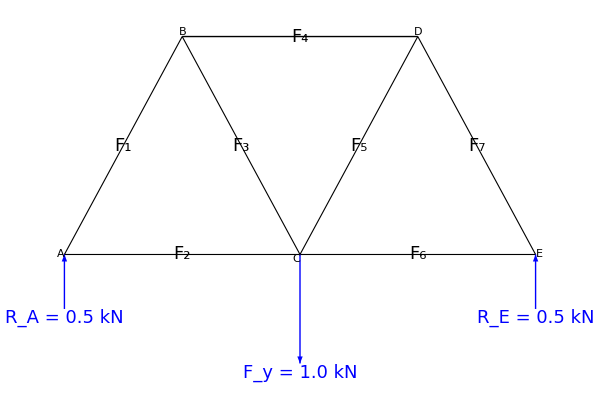

```mathematica
Module[{w,h,θ,Fy,sol,RE,RA},
w=1;h=w/2*Tan[θ];θ=60°;Fy=1;

sol=Quiet@Solve[{w*Fy+2*w*(-re)==0,ra-Fy+re==0},{ra,re}][[1]];
RE=re/.sol;RA=ra/.sol;

Graphics[{Thick,
{EdgeForm@Thick,FaceForm@None,Polygon[{{0,0},{w,0},{0.5*w,h}}],Polygon[{{w,0},{2*w,0},{1.5*w,h}}]},
Line[{{0.5*w,h},{1.5*w,h}}],

{Blue,Arrow[{{0,-0.25*h},{0,0}}],Arrow[{{w,0},{w,-0.5*h}}],Arrow[{{2*w,-0.25*h},{2*w,0}}],
Text[Style[Row@{var["R",#1,Blue]," = ",NumberForm[N@#2,{3,1}]," kN"},18],#3,{0,1.5}]&@@@{{"A",RA,{0,-0.25*h}},{"E",RE,{2*w,-0.25*h}}},
Text[Style[Row@{var["F","y",Blue]," = ",NumberForm[N@Fy,{3,1}]," kN"},18],{w,-0.5*h},{0,1.5}]},

Text[Style[Subscript[Style["F",Italic],#1],18,Background->White],#2]&@@@{
{1,{0.25*w,0.5*h}},{2,{0.5*w,0}},{3,{0.75*w,0.5*h}},{4,{w,h}},{5,{1.25*w,0.5*h}},{6,{1.5*w,0}},{7,{1.75*w,0.5*h}}},

Text[Framed[Style[Row@{" ",#1," "},16],RoundingRadius->15],#2,1.2*#3]&@@@{
{"A",{0,0},{1,0}},{"B",{0.5*w,h},{0,-1}},{"C",{w,0},{1,1}},{"D",{1.5*w,h},{0,-1}},{"E",{2*w,0},{-1,0}}}
},ImageSize->{600,400}]
]
```